# Assignment 1 Shivansh Tomar

## Q1 peculiar velocity

```mathematica
d = List[38.8, 60.6, 73.8, 87, 140.4, 268.7]
```

{38.8,60.6,73.8,87,140.4,268.7}

```mathematica
z = 299792.458*List[.01, .012, .016, .02167, .0343, .0593]
```

{2997.92,3597.51,4796.68,6496.5,10282.9,17777.7}

```mathematica
data = Transpose@{d,z}
```

{{38.8,2997.92},{60.6,3597.51},{73.8,4796.68},{87,6496.5},{140.4,10282.9},{268.7,17777.7}}

```mathematica
line = Fit[data,{1,x},x]
```

267.193+66.2573 x

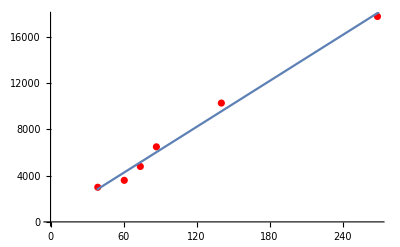

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[line,{x,38,270}]]
```

```mathematica
3.08567758128 10^(19)/70
```

4.40811×10^17

```mathematica
4.408 10^(17)*3.171*10^(-8)
```

1.39778×10^10

## Q2 Age of universe

```mathematica
H[z_]:=Sqrt[0.2+0.8(1+z)^3+10^(-4)(1+z)^4]
```

```mathematica
Ct = Table[NIntegrate[1/(H[z](1+z)),{z,i,∞}],{i,{0,2,6,1100}}]
```

{0.717217,0.143145,0.0401898,0.0000178547}

```mathematica
Rs =List[0.01,2,6,1100]
```

{0.01,2,6,1100}

```mathematica
CT = Transpose@{Rs,Ct}
```

{{0.01,0.717217},{2,0.143145},{6,0.0401898},{1100,0.0000178547}}

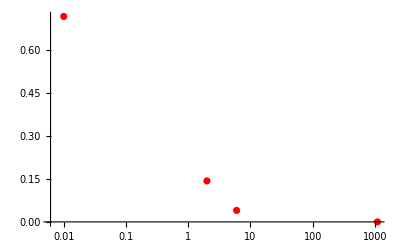

```mathematica
ListLogLinearPlot[CT,PlotStyle->Red]
```

## Q3 Look Back time

```mathematica
H[z_]:=Sqrt[0.2+0.8(1+z)^3+10^(-4)(1+z)^4]
```

```mathematica
Ct = Table[NIntegrate[1/(H[z](1+z)),{z,0,i}],{i,{0,2,6,1100}}]
```

{0.,0.574072,0.677027,0.717199}

```mathematica
Rs =List[0.01,2,6,1100]
```

{0.01,2,6,1100}

```mathematica
CT = Transpose@{Rs,Ct}
```

{{0.01,0.},{2,0.574072},{6,0.677027},{1100,0.717199}}

```mathematica
ListLogLinearPlot[CT,PlotStyle->Red]
```

-Graphics-

## Q5

```mathematica
H[z_]:=Sqrt[0.7+0.3(1+z)^3+188(1+z)^4]
```

```mathematica
Ld = Table[(1+i)NIntegrate[1/H[z],{z,0,i}],{i,{0,2,6,1100}}]
```

{0.,0.145707,0.437206,80.1639}

```mathematica
Cd= Table[NIntegrate[1/H[z],{z,0,i}],{i,{0,2,6,1100}}]
```

{0.,0.0485689,0.062458,0.0728101}

```mathematica
Ad = Table[1/(1+i)NIntegrate[1/H[z],{z,0,i}],{i,{0,2,6,1100}}]
```

{0.,0.0161896,0.00892258,0.0000661309}

```mathematica
Rs =List[0.01,2,6,1100]
```

{0.01,2,6,1100}

```mathematica
LD = Transpose@{Rs,Ld};
CD = Transpose@{Rs,Cd};
AD = Transpose@{Rs,Ad};
```

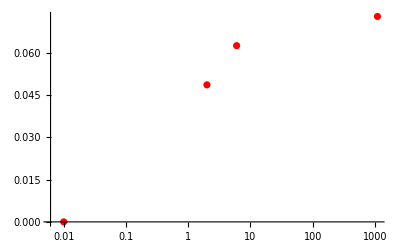

```mathematica
ListLogLinearPlot[CD,PlotStyle->Red]
```

```mathematica
ListLogLinearPlot[{LD,CD,AD},PlotLabels->{"LD","CD","AD"}]
```

-Graphics-

## Q7

```mathematica
B[z_,T_,ν_]:=1/(1+z)^3 ν^3/(Exp[0.0005*ν/T]-1)
```

```mathematica
LogLinearPlot[{B[0,2.7,ν],B[6,2.7,ν],B[20,2.7,ν],B[1090,2.7,ν],B[10^4,2.7,ν]},{ν,1,10^5},PlotLabels->{"z=0","z=6","z=20","z=1090","z=10^4"}]
```

-Graphics-

```mathematica
4.79924307×10^(-11+7)
```

0.000479924

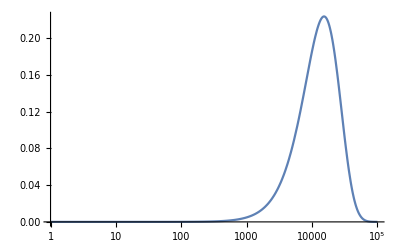

```mathematica
LogLinearPlot[B[10^4,2.7,ν],{ν,1,10^5}]
```

```mathematica
(2/8)^(1/3)-1
```

-1+1/2^(2/3)

```mathematica
N[-1+1/2^(2/3)]
```

-0.370039

```mathematica
N[-1+(7/3)^(1/3)]
```

0.326352

```mathematica
N[(2000)^(1/4)-1]
```

5.6874